```mathematica
sched = SemanticImport["/Users/erichegonzales/Downloads/EventSearch Result - DaySmart Rec Admin-3.csv"]
```

```mathematica
schedByWeek = sched[GroupBy["Start Date"]]
```

```mathematica
schedByWeek[DateObject[{2024,4,4},"Day"]]
```

```mathematica
date = FromDateString["4/25/24"]
```

```mathematica
Normal[schedByWeek][DateObject[{2024,4,4},"Day"]];
```

```mathematica
matchups = Map[StringSplit [#, " vs "]&, sched[All, "Description"]]
```

```mathematica
matchupsByWeek
```

```mathematica
Flatten[matchupsByWeek]
```

```mathematica
allteams = Union[Normal[matchups[All, 1]]]
```

{Team 10 (Tar Heels),Team 11 (Cavaliers),Team 12 (Ducks),Team 13 (Bears),Team 14 (Hawks),Team 1 (Gophers),Team 2 (Tigers),Team 3 (Spartans),Team 4 (Wolfpack),Team 5 (Bulldogs),Team 6 (Wildcats),Team 7 (Red Storm),Team 8 (Eagles),Team 9 (Huskies)}

```mathematica
divValues = {"West", "West/East", "East", "East", "West", "West", "East", "West", "West/East", "West", "West", "East", "East", "East"}
```

{West,West/East,East,East,West,West,East,West,West/East,West,West,East,East,East}

```mathematica
divs =AssociationThread[teams, divValues]
```

<|Team 10 (Tar Heels)→West,Team 11 (Cavaliers)→West/East,Team 12 (Ducks)→East,Team 13 (Bears)→East,Team 14 (Hawks)→West,Team 1 (Gophers)→West,Team 2 (Tigers)→East,Team 3 (Spartans)→West,Team 4 (Wolfpack)→West/East,Team 5 (Bulldogs)→West,Team 6 (Wildcats)→West,Team 7 (Red Storm)→East,Team 8 (Eagles)→East,Team 9 (Huskies)→East|>

```mathematica
eastTeams = Select[divs, #== "East"&]
westTeams = Select[divs, #== "West"&]
centTeams = Select[divs, #== "East/West"||#=="West/East"&]
styles = Join[Map[#-> Green&, Keys[eastTeams]], Map[#-> Yellow&, Keys[centTeams]], Map[#-> Red&, Keys[westTeams]]]
```

```mathematica
matchupsByWeek = Map[StringSplit [#, " vs "]&, Normal[schedByWeek][date][[All, "Description"]]]
```

```mathematica
edges = Map[#[[1]] <-> #[[2]] &, matchupsByWeek]
```

```mathematica
matchupsByWeek[[1]]
```

```mathematica
test =Map[{divs[#[[1]]], divs[#[[2]]]}&, matchupsByWeek]
```

```mathematica
StringContainsQ[test[[3]][[1]], test[[3]][[2]]]
```

```mathematica
badMatchups = Map[StringContainsQ[divs[#[[1]]], divs[#[[2]]]]&, matchupsByWeek]
```

```mathematica
badMatchups = Select[matchupsByWeek, !StringContainsQ[divs[#[[1]]], divs[#[[2]]]]&]
```

```mathematica
badEdges = #1<->#2&@@@badMatchups
```

```mathematica
g = Graph[edges]
```

```mathematica
GraphPlot[g, ContentSelectable->True]
```

```mathematica
Graph[{1<->2,2<->3,3<->1}]
```

```mathematica
testSave = 1
```

```mathematica
TableView[{{1, 2, 3}}]
```

```mathematica
Needs["GraphUtilities`"]
```

```mathematica
GraphEdit[]
```

```mathematica
GraphEdit[]
```

```mathematica
swap[i_,j_]:=(a=ReplacePart[a,{i->a[[j]],j->a[[i]]}])
```

```mathematica
ResourceFunction["DarkMode"][]
```

```mathematica
ng = SemanticImport["/Users/erichegonzales/Downloads/Schedule Adjuster - Sheet1-4.csv"]
```

```mathematica
byDate = ng[GroupBy["Date"]]
```

```mathematica
week = Normal[byDate][FromDateString["4/25/24"]]
```

{<|Date→Thu 25 Apr 2024,Home Team→Team 2 (Tigers),Away Team→Team 8 (Eagles)|>,<|Date→Thu 25 Apr 2024,Home Team→Team 4 (Wolfpack),Away Team→Team 10 (Tar Heels)|>,<|Date→Thu 25 Apr 2024,Home Team→Team 7 (Red Storm),Away Team→Team 9 (Huskies)|>,<|Date→Thu 25 Apr 2024,Home Team→Team 1 (Gophers),Away Team→Team 6 (Wildcats)|>,<|Date→Thu 25 Apr 2024,Home Team→Team 3 (Spartans),Away Team→Team 5 (Bulldogs)|>}

```mathematica
teams = Union[Join[week[[All, "Home Team"]], week[[All, "Away Team"]]]]
```

{Team 10 (Tar Heels),Team 1 (Gophers),Team 2 (Tigers),Team 3 (Spartans),Team 4 (Wolfpack),Team 5 (Bulldogs),Team 6 (Wildcats),Team 7 (Red Storm),Team 8 (Eagles),Team 9 (Huskies)}

```mathematica
weekEdges = #["Home Team"]<->#["Away Team"]&/@ week
```

{Team 2 (Tigers)<->Team 8 (Eagles),Team 4 (Wolfpack)<->Team 10 (Tar Heels),Team 7 (Red Storm)<->Team 9 (Huskies),Team 1 (Gophers)<->Team 6 (Wildcats),Team 3 (Spartans)<->Team 5 (Bulldogs)}

```mathematica
teams = Union[Normal[Join[ng[All, "Home Team"], ng[All, "Away Team"]]]]
```

{Team 10 (Tar Heels),Team 11 (Cavaliers),Team 12 (Ducks),Team 13 (Bears),Team 14 (Hawks),Team 1 (Gophers),Team 2 (Tigers),Team 3 (Spartans),Team 4 (Wolfpack),Team 5 (Bulldogs),Team 6 (Wildcats),Team 7 (Red Storm),Team 8 (Eagles),Team 9 (Huskies)}

```mathematica
Union[Join[Normal[ng[All, "Home Team"], ng[All, "Away Team"]]]]
```

```mathematica
newEdges = Normal[Map[#[["Home Team"]] <-> #[["Away Team"]] &, ng]]
```

{Team 12 (Ducks)<->Team 6 (Wildcats),Team 14 (Hawks)<->Team 4 (Wolfpack),Team 2 (Tigers)<->Team 3 (Spartans),Team 10 (Tar Heels)<->Team 8 (Eagles),Team 1 (Gophers)<->Team 9 (Huskies),Team 13 (Bears)<->Team 5 (Bulldogs),Team 11 (Cavaliers)<->Team 7 (Red Storm),Team 3 (Spartans)<->Team 13 (Bears),Team 8 (Eagles)<->Team 1 (Gophers),Team 5 (Bulldogs)<->Team 11 (Cavaliers),Team 14 (Hawks)<->Team 2 (Tigers),Team 9 (Huskies)<->Team 7 (Red Storm),Team 4 (Wolfpack)<->Team 12 (Ducks),Team 6 (Wildcats)<->Team 10 (Tar Heels),Team 9 (Huskies)<->Team 5 (Bulldogs),Team 7 (Red Storm)<->Team 1 (Gophers),Team 10 (Tar Heels)<->Team 4 (Wolfpack),Team 8 (Eagles)<->Team 6 (Wildcats),Team 11 (Cavaliers)<->Team 3 (Spartans),Team 12 (Ducks)<->Team 2 (Tigers),Team 13 (Bears)<->Team 14 (Hawks),Team 2 (Tigers)<->Team 8 (Eagles),Team 4 (Wolfpack)<->Team 10 (Tar Heels),Team 7 (Red Storm)<->Team 9 (Huskies),Team 1 (Gophers)<->Team 6 (Wildcats),Team 3 (Spartans)<->Team 5 (Bulldogs),Team 10 (Tar Heels)<->Team 3 (Spartans),Team 5 (Bulldogs)<->Team 1 (Gophers),Team 11 (Cavaliers)<->Team 4 (Wolfpack),Team 7 (Red Storm)<->Team 13 (Bears),Team 6 (Wildcats)<->Team 14 (Hawks),Team 9 (Huskies)<->Team 2 (Tigers),Team 8 (Eagles)<->Team 12 (Ducks),Team 9 (Huskies)<->Team 12 (Ducks),Team 5 (Bulldogs)<->Team 6 (Wildcats),Team 8 (Eagles)<->Team 7 (Red Storm),Team 10 (Tar Heels)<->Team 11 (Cavaliers),Team 13 (Bears)<->Team 2 (Tigers),Team 14 (Hawks)<->Team 4 (Wolfpack),Team 1 (Gophers)<->Team 3 (Spartans),Team 4 (Wolfpack)<->Team 6 (Wildcats),Team 2 (Tigers)<->Team 7 (Red Storm),Team 8 (Eagles)<->Team 9 (Huskies),Team 13 (Bears)<->Team 12 (Ducks),Team 14 (Hawks)<->Team 10 (Tar Heels),Team 3 (Spartans)<->Team 11 (Cavaliers),Team 5 (Bulldogs)<->Team 1 (Gophers)}

```mathematica
getStyle[teams_]:= If[divs[#] == "West", #-> Red, If[divs[#] == "East", #-> Green, If[divs[#] == "West/East", #-> Yellow]]]& /@ teams
```

```mathematica
getStyle[teams]
```

{Team 10 (Tar Heels)→RGBColor[1, 0, 0],Team 11 (Cavaliers)→RGBColor[1, 1, 0],Team 12 (Ducks)→RGBColor[0, 1, 0],Team 13 (Bears)→RGBColor[0, 1, 0],Team 14 (Hawks)→RGBColor[1, 0, 0],Team 1 (Gophers)→RGBColor[1, 0, 0],Team 2 (Tigers)→RGBColor[0, 1, 0],Team 3 (Spartans)→RGBColor[1, 0, 0],Team 4 (Wolfpack)→RGBColor[1, 1, 0],Team 5 (Bulldogs)→RGBColor[1, 0, 0],Team 6 (Wildcats)→RGBColor[1, 0, 0],Team 7 (Red Storm)→RGBColor[0, 1, 0],Team 8 (Eagles)→RGBColor[0, 1, 0],Team 9 (Huskies)→RGBColor[0, 1, 0]}

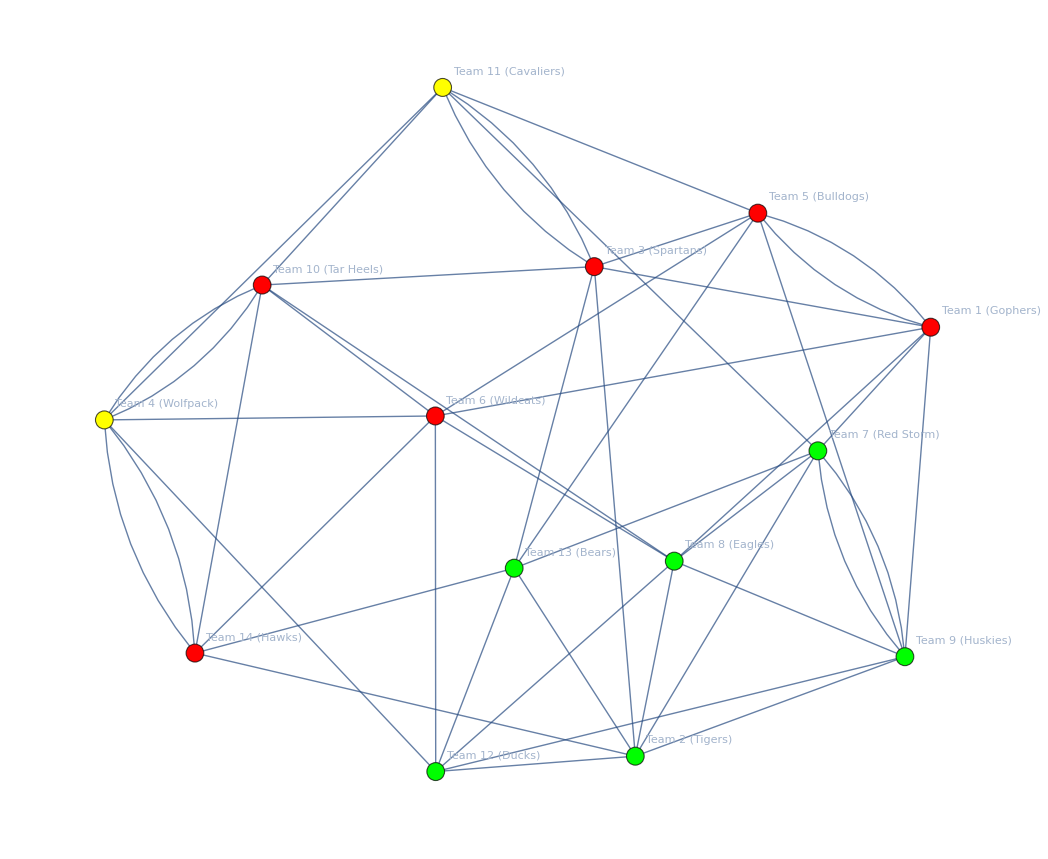

```mathematica
totG = Graph[allteams, newEdges, VertexLabels->"Name", VertexStyle->getStyle[allteams]]
```

```mathematica
coords = GraphEmbedding[totG]
```

{{0.463843,1.41014},{0.994176,1.98288},{0.97378,0.},{1.20441,0.589443},{0.266288,0.343419},{2.4284,1.28791},{1.56032,0.0445893},{1.43971,1.4635},{0.,1.01925},{1.92041,1.61846},{0.972722,1.03065},{2.09678,0.929598},{1.67469,0.609855},{2.35258,0.332981}}

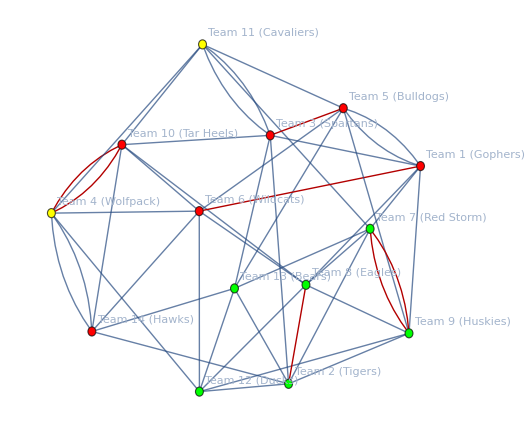

```mathematica
weekG = Graph[allteams, newEdges, VertexLabels->"Name",EdgeStyle->Thin, VertexStyle->getStyle[allteams], VertexCoordinates->coords, GraphHighlight->weekEdges, GraphHighlightStyle->"Thick"]
```

```mathematica
ResourceFunction["DarkMode"][False]
```